# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
(*Get["../../neupackage/mma/neutrino.wl"]*)
Get["https://raw.githubusercontent.com/NeuPhysics/neupackage/master/mma/neutrino.wl"]
```

```mathematica
(*Get["../../neupackage/mma/neumat.wl"]*)
Get["https://raw.githubusercontent.com/NeuPhysics/neupackage/master/mma/neumat.wl"]
```

```mathematica
colorpalette5={RGBColor[172,151,62],
RGBColor[129,118,204],
RGBColor[91,169,102],
RGBColor[199,90,147],
RGBColor[204,95,67]}
```

{RGBColor[172,151,62],RGBColor[129,118,204],RGBColor[91,169,102],RGBColor[199,90,147],RGBColor[204,95,67]}

```mathematica
markers=Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

## Rabi Oscillation

```mathematica
ampRabi[a_,k_,omegam_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2);
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

## Parameters

Parameters

```mathematica
endpoint=400000;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
?OmegaVacuum
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2
```

Takes [energy_,deltam2_] as parameters and calculates ω_v. Should becareful about units.

1.3×10^-16

0.154948

```mathematica
fraction=0.5(*0.99*)
lambdaN=fraction*Cos[2thetaV]omegaV (*MeV*)
```

0.5

6.19038×10^-17

```mathematica
thetamVN=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
```

```mathematica
omegaV=OmegaVacuum[energy20,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)
lambdaN=0.5*Cos[2thetaV]omegaV (*MeV*)
omegaM=OmegaMatter2[lambdaN,thetaV,omegaV](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi]
```

6.5×10^-17

3.09519×10^-17

3.67552×10^-17

0.198931

```mathematica
datafracStashFullTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

## Destruction Criteria

```mathematica
q2a[q_,k_]:=(k-1)/q;
q2deltak[q_,a_]:=a q;
qvalue[a_,k_]:=Abs[(k-1)/a]
```

We can define the non-approximate formula for relative detuning

## Numerical Solutions

```mathematica
solSingleNum[k_,a_,endpointModule_]:=Module[
{sysM},

sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(a Cos[2thetamV]Sin[k x])PauliMatrix[3]/2-(a Sin[2thetamV] Sin[k x])PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

NDSolve[sysM,{psi1,psi2},{x,0,endpointModule},AccuracyGoal->2$MachinePrecision]
]
```

Listarize the solutions

```mathematica
solutionLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
```

Calculate the gridnlies

### A List of parameters

```mathematica
q2deltak[1,10^(-4)Sin[2thetamV]/2]
```

0.0000193725

```mathematica
k11=1;
a11=10^(-4);

k12=1-0.00001
a12=10^(-4)

(*k13=1-0.00002
a13=10^(-4)
*)
k13=1-0.5
a13=5 1/1000


k14=1-0.0001
a14=10^(-4)
```

0.99999

1/10000

0.5

1/200

0.9999

1/10000

Construct the full list of k’s and a’s to test

```mathematica
(*kList={k11,k12,k13,k14};
aList={a11,a12,a13,a14};
*)

kList={k13};
aList={a13};
```

```mathematica
Table[qvalue[aList[[i]] Sin[2thetamV]/2,kList[[i]]],{i,1,Length@kList}]
```

{516.197}

### The solutions are

```mathematica
solSingleNumAll=Table[
solSingleNum[kList[[i]],aList[[i]],endpoint],
{i,1,Length@kList}]
```

{{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}}}

The following is some test for each individual

### Theory

```mathematica
theoryProbList=Table[
Table[{x,probRabi[aList[[i]]Sin[2thetamV]/2,kList[[i]],1,x]},{x,0,endpoint,endpoint/50}]
,{i,1,Length@kList}];
theoryAmpList=Table[
ampRabi[aList[[i]]Sin[2thetamV]/2,kList[[i]],1]
,{i,1,Length@kList}];
```

### Visualziation of the solutions

```mathematica
sols=solutionLists[solSingleNumAll,endpoint,1000];
```

```mathematica
plotleg=Table["k="<>ToString[N@kList[[i]]]<>";a="<>ToString[N@aList[[i]]]<>";",{i,1,Length@kList}]
(*plotmarkers={""," ","  ","   ",{"○",11},{"□",13},{"◇",13},{"△",13},{"+",18},{"○",11.136}}*)
plotmarkers={"",{"○",11},{"□",13},{"◇",13},{"△",13},{"+",18},{"○",11.136}}
```

{k=0.5;a=0.005;}

{,{○,11},{□,13},{◇,13},{△,13},{+,18},{○,11.136}}

List plot of the results

```mathematica
ListPlot[
Join[sols,theoryProbList]
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks}},PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},Joined->Join[Table[True,{i,1,Length@kList}],Table[False,{i,1,Length@kList}]],
PlotMarkers->plotmarkers,
PlotStyle->{Black,Directive[Red,Dotted],Blue,Magenta},PlotLegends->Placed[plotleg,{Center,Below}],GridLines->{None, {1,0.5}}]
```

-Graphics-

```mathematica
Export["export/test-fail-rabi-formula-5.pdf",%]
```

export/test-fail-rabi-formula-5.pdf

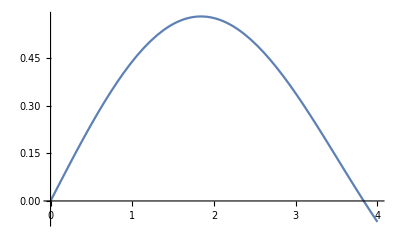

```mathematica
Plot[BesselJ[1,z],{z,0,4}]
```

```mathematica
Solve[Cos[2thetamV]a13x/k13==2,a13x]
```

{{a13x→1.08473}}

### Export Data

```mathematica
Table[
Export["../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-a1-"<>ToString[N@aList[[i]]]<>"-k1-"<>ToString[kList[[i]]]<>".csv",sols[[i]]]
,{i,1,Length@kList}]
```

{../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-a1-0.0001-k1-1.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-a1-0.0001-k1-0.99999.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-a1-0.0001-k1-0.99998.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-a1-0.0001-k1-0.9999.csv}

```mathematica
Table[
Export["../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-theory-prob-a1-"<>ToString[N@aList[[i]]]<>"-k1-"<>ToString[kList[[i]]]<>".csv",theoryProbList[[i]]]
,{i,1,Length@kList}]
```

{../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-theory-prob-a1-0.0001-k1-1.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-theory-prob-a1-0.0001-k1-0.99999.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-theory-prob-a1-0.0001-k1-0.99998.csv,../../ipynb/papers/assets/single-frequency/paper-single-frequency-simple-theory-prob-a1-0.0001-k1-0.9999.csv}

Export the  Rabi formula fail case

```mathematica
(*Table[
Export["export/paper-single-frequency-simple-a1-"<>ToString[N@aList[[i]]]<>"-k1-"<>ToString[kList[[i]]]<>".csv",sols[[i]]]
,{i,1,Length@kList}]
Table[
Export["export/paper-single-frequency-simple-theory-prob-a1-"<>ToString[N@aList[[i]]]<>"-k1-"<>ToString[kList[[i]]]<>".csv",theoryProbList[[i]]]
,{i,1,Length@kList}]*)
```

Modes Using Jacobi-Anger Expansion and Relative Detunings

We expand the system using Jacobi-Anger expansion and investigate the relative detunings.

```mathematica
listNGenerator[1,3]
```

{{-3,3}}

```mathematica
kList
```

{0.99998}

```mathematica
widthNList[qvalueList4Paper[[2,1]],{kList[[4]]},{aList[[4]]},{0,0},thetamV]
```

Part::partw: Part 4 of {0.99998} does not exist.

Part::partw: Part 4 of {1/100} does not exist.

Part::partw: Part 4 of {0.01} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

0.420276 Abs[BesselJ[1,(0.921891 {1/100}⟦4⟧)/({0.99998}⟦4⟧)] {0.99998}⟦4⟧]

```mathematica
whichk=3;
qvalueList4Paper=qValueOrderdList[listNGenerator[1,60],{kList[[whichk]]},{aList[[whichk]]},{0},thetamV];
neuWidthList4Paper=Table[widthNList[qvalueList4Paper[[i,1]],{kList[[whichk]]},{aList[[whichk]]},{0},thetamV],{i,1,Length@qvalueList4Paper}];
neuGridList4Paper=Table[
{qvalueList4Paper[[i,1]],
qvalueList4Paper[[i,2]],
neuWidthList4Paper[[i]],
qvalueList4Paper[[1,2]]+neuWidthList4Paper[[i]]/(2 neuWidthList4Paper[[1]]qvalueList4Paper[[i,2]]),
2Pi/(neuWidthList4Paper[[i]]^2+(1-qvalueList4Paper[[i,1]].{kList[[whichk]]})^2)^(1/2)},
{i,1,Length@qvalueList4Paper}];
PrependTo[neuGridList4Paper,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Part[%,1;;10]//Grid
```

Part::partw: Part 3 of {0.99998} does not exist.

Part::partw: Part 3 of {1/100} does not exist.

Part::partw: Part 3 of {0.99998} does not exist.

Part::partw: Part 3 of {1/100} does not exist.

Part::partw: Part 3 of {0.01} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 3 of {0.99998} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{-1} | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 0.420276 Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(0.210138 Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧])/Abs[-1-{0.99998}⟦3⟧] | (2 π)/(√(0.176632 Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+{0.99998}⟦3⟧)^2))
{1} | (2.37939 Abs[-1+{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {1/100}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 0.420276 Abs[BesselJ[1,(0.921891 {1/100}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(0.210138 Abs[BesselJ[1,(0.921891 {1/100}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1+{0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(0.176632 Abs[BesselJ[1,(0.921891 {1/100}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1-{0.99998}⟦3⟧)^2))
{-2} | (1.18969 Abs[-1-2 {0.99998}⟦3⟧])/Abs[BesselJ[2,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 0.840553 Abs[BesselJ[2,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(0.840553 Abs[BesselJ[2,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-2 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(0.706529 Abs[BesselJ[2,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+2 {0.99998}⟦3⟧)^2))
{-3} | (0.793129 Abs[-1-3 {0.99998}⟦3⟧])/Abs[BesselJ[3,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 1.26083 Abs[BesselJ[3,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(1.89124 Abs[BesselJ[3,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-3 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(1.58969 Abs[BesselJ[3,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+3 {0.99998}⟦3⟧)^2))
{-4} | (0.594847 Abs[-1-4 {0.99998}⟦3⟧])/Abs[BesselJ[4,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 1.68111 Abs[BesselJ[4,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(3.36221 Abs[BesselJ[4,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-4 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(2.82612 Abs[BesselJ[4,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+4 {0.99998}⟦3⟧)^2))
{-5} | (0.475877 Abs[-1-5 {0.99998}⟦3⟧])/Abs[BesselJ[5,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 2.10138 Abs[BesselJ[5,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(5.25345 Abs[BesselJ[5,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-5 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(4.4158 Abs[BesselJ[5,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+5 {0.99998}⟦3⟧)^2))
{-6} | (0.396564 Abs[-1-6 {0.99998}⟦3⟧])/Abs[BesselJ[6,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 2.52166 Abs[BesselJ[6,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(7.56497 Abs[BesselJ[6,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-6 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(6.35876 Abs[BesselJ[6,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+6 {0.99998}⟦3⟧)^2))
{-7} | (0.339912 Abs[-1-7 {0.99998}⟦3⟧])/Abs[BesselJ[7,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 2.94193 Abs[BesselJ[7,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(10.2968 Abs[BesselJ[7,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-7 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(8.65498 Abs[BesselJ[7,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+7 {0.99998}⟦3⟧)^2))
{-8} | (0.297423 Abs[-1-8 {0.99998}⟦3⟧])/Abs[BesselJ[8,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | 3.36221 Abs[BesselJ[8,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧] | (2.37939 Abs[-1-{0.99998}⟦3⟧])/Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]+(13.4488 Abs[BesselJ[8,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2)/(Abs[-1-8 {0.99998}⟦3⟧] Abs[BesselJ[1,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]) | (2 π)/(√(11.3045 Abs[BesselJ[8,(0.921891 {0.01}⟦3⟧)/({0.99998}⟦3⟧)] {0.99998}⟦3⟧]^2+(1+8 {0.99998}⟦3⟧)^2))

```mathematica
Table[
2Pi/(widthNList[{qvalueList4Paper[[n,1,1]]},{First@kList},{First@aList},{0},thetamV] √(1+qvalueList4Paper[[n,2]]^2))
,{n,1,4}]
```

{61685.,3.14175,6.28507,2.09474}

What to test

The function has been tested. Now for two frequencies, what should we test?